# Project report

## From GC temperature program to algebraic function

D Malan

Department of Chemistry
University of Pretoria

14 February 2020

## Introduction

To improve the repeatability of the coaxial heater temperature set point during fast GC runs, it is necessary to convert the temperature program into a mathematical function. (See the report Set point misbehaviour: the causes.)

There must be many ways to describe a GC temperature program, but the chromatography community seem to have converged on the concept of ramps and holds. This is the idea used in the SFCxGC control software. This software is written in LabVIEW, and the temperature program is stored as an array of structures. Each structure contains three elements: a ramp rate, a target temperature and a hold time.

When the temperature program is not running the set point is determined by other controls on the VI front panel, like “GC idle temperature” and “Purge temperature”.

## Calculations

Earlier I developed the method, showing the work, but I lost the file. I will show the resulting ideas here. Consider a temperature program with three sections, each with a rate (r), a final temperature, or level (l) and a hold time (h).

```mathematica
tprog ={{r1,l1,h1},{r2, l2, h2},{r3, l3, h3}}
```

{{r1,l1,h1},{r2,l2,h2},{r3,l3,h3}}

The first task is to convert these to a series of times, which represent the sections of the piecewise function. All that are required are the start end end times of either the hold or the ramp. Because the first section of the program does not actually have a ramp (it represents the starting temperature), I choose to calculate the start and end times for each hold. These are in the form of a list, with each section of the program getting an entry.

The duration of the ramp is the difference between the levels of the two consecutive sections, divided by the rate.

```mathematica
t1 = {0,h1};
t2 =t1[[2]]+(l2-l1)/r2+{0,h2};
t3 = t2[[2]]+(l3-l2)/r3+{0,h3};
```

The five polynomials for the program are:

```mathematica
p1 = l1;
p2 = l1+r2*(t-t1[[2]]);
p3 = l2;
p4 = l2 + r3*(t-t2[[2]]);
p5 = l3;
```

```mathematica
p = Piecewise[{
{p1, t1[[1]]≤ t<t1[[2]] }
,{p2,t1[[2]]≤ t< t2[[1]]}
,{p3,t2[[1]]≤ t< t2[[2]]}
,{p4, t2[[2]]≤ t< t3[[1]]}
,{p5,t3[[1]]≤ t< t3[[2]]}
}]
```

Piecewise[{{l1, 0≤t<h1}, {l1+r2 (-h1+t), h1≤t<h1+(-l1+l2)/r2}, {l2, h1+(-l1+l2)/r2≤t<h1+h2+(-l1+l2)/r2}, {l2+r3 (-h1-h2-(-l1+l2)/r2+t), h1+h2+(-l1+l2)/r2≤t<h1+h2+(-l1+l2)/r2+(-l2+l3)/r3}, {l3, h1+h2+(-l1+l2)/r2+(-l2+l3)/r3≤t<h1+h2+h3+(-l1+l2)/r2+(-l2+l3)/r3}, {0, True}}]

Give the variables some values:

```mathematica
r1 = 0; l1 = -25; h1 = 2/60.;
r2 = 8000.; l2 = 60; h2 = 2/60.;
r3 = 2000.; l3 = 350; h3 =2/60.;
```

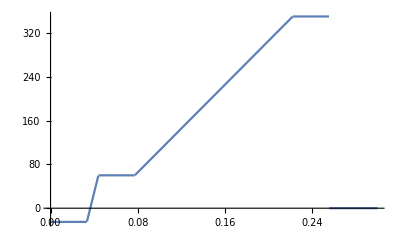

```mathematica
Plot[p, {t, 0,0.3}]
```

```mathematica
p
```

Piecewise[{{-25, 0≤t<0.0333333}, {-25+8000. (-0.0333333+t), 0.0333333≤t<0.0439583}, {60, 0.0439583≤t<0.0772917}, {60+2000. (-0.0772917+t), 0.0772917≤t<0.222292}, {350, 0.222292≤t<0.255625}, {0, True}}]

This function will give the intended set point as a function of time.

## Results

```mathematica
r1 = 0; l1 = -25; h1 = 2/60.;
r2 = 8000.; l2 = 60; h2 = 2/60.;
r3 = 2000.; l3 = 350; h3 =2/60.;
```

```mathematica
Plot[p, {t, 0,0.3}]
```

-Graphics-

## Discussion

The method used above can describe the temperature program of a fast chromatogram as a function of time. It is scalable and amenable to a conventional iterative approach.

It might not even be necessary to write a piecewise function in LabVIEW. Because the piecewise function consists of zeroth and first-order polynomials, i.e. straight line segments, it would be possible to use linear interpolation from a simple array. LabVIEW has handy library functions for interpolations. It might even be possible to use cubic Hermite interpolation. This is apparently continuous in the first derivate, and the controller will like that very much. 
-Graphics--Graphics-

## Conclusion

A method has been described that can convert a gas chromatographic temperature program expressed as a collection of rates, ramp final temperatures and hold times as a piecewise polynomial function of time elapsed since the start of the temperature program. This function can be implemented either as a piecewise function or as an interpolation.

## Recommendations

Implement this function in LabVIEW.

If possible, use cubic Hermite interpolation.